```mathematica
(* Transition density *)
```

```mathematica
f[y_]:=(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x]
```

```mathematica
(* first partial derivative *)
```

```mathematica
D[f[y],{y,1}]
```

-ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^(3/2) √(2/π) (g1-x)-(ⅇ^(-1/2 n (-x+y)^2) (1-ⅇ^(-2 n (g1-x) (g2-y))) n^(3/2) (-x+y))/(√(2 π))

```mathematica
(* First partial derivative*)
```

```mathematica
d1[x_,y_]:=-ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^(3/2) √(2/π) (g1-x)-(ⅇ^(-1/2 n (-x+y)^2) (1-ⅇ^(-2 n (g1-x) (g2-y))) n^(3/2) (-x+y))/(√(2 π))
```

```mathematica
(* removing the part the gets removed by y -> g2*)
```

```mathematica
d1d[x_,y_]:=-ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^(3/2) √(2/π) (g1-x)
```

```mathematica
(*Some type of symmetry?*)
```

```mathematica
Plot3D[{d1[x,y]/.g1->0.4 /.g2->1/.n->3,d1d[x,y]/.g1->0.4/.g2->1/.n->3,d1[x,1]/.g1->0.4/.g2->1/.n->3},{x,-3,0.4},{y,-3,1},PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[{d1[x,y]-d1d[x,y]/.g1->1 /.g2->1/.n->130},{x,-1,1},{y,-1,1},PlotRange->Full]
```

-Graphics3D-

```mathematica
(* 4th partial derivative used in EMSF *)
```

```mathematica
D[f[y],{y,4}]
```

1/(√(2 π))√n (-16 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^4 (g1-x)^4+32 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^4 (g1-x)^3 (-x+y)-24 ⅇ^(-2 n (g1-x) (g2-y)) n^2 (g1-x)^2 (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)-8 ⅇ^(-2 n (g1-x) (g2-y)) n (g1-x) (3 ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)-ⅇ^(-1/2 n (-x+y)^2) n^3 (-x+y)^3)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (3 ⅇ^(-1/2 n (-x+y)^2) n^2-6 ⅇ^(-1/2 n (-x+y)^2) n^3 (-x+y)^2+ⅇ^(-1/2 n (-x+y)^2) n^4 (-x+y)^4))

```mathematica
(* Riemann sum approximation of integral of 4th partial derivativeb*)
```

```mathematica
riemannsum =Table[1/n^0.01*∑_(k=-4*n^0.01)^(1*n^0.01) (1/(√(2 π))√n (-16 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^4 (g1-x)^4+32 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^4 (g1-x)^3 (-x+y)-24 ⅇ^(-2 n (g1-x) (g2-y)) n^2 (g1-x)^2 (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)-8 ⅇ^(-2 n (g1-x) (g2-y)) n (g1-x) (3 ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)-ⅇ^(-1/2 n (-x+y)^2) n^3 (-x+y)^3)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (3 ⅇ^(-1/2 n (-x+y)^2) n^2-6 ⅇ^(-1/2 n (-x+y)^2) n^3 (-x+y)^2+ⅇ^(-1/2 n (-x+y)^2) n^4 (-x+y)^4)) /. y-> k/n^0.01  /.x-> 0.9 /. g1->1 +1/n/.g2-> 1)//N,{n,1,500,5}]
```

{0.973627,206.356,924.292,2147.66,3782.92,5503.05,6891.62,7558.77,7199.93,5618.54,2722.67,-1493.05,-6970.24,-13607.5,-21275.6,-29827.,-39099.8,-48919.3,-59097.5,-69433.3,-79713.9,-89716.9,-99215.4,-107983.,-115801.,-122463.,-127784.,-131605.,-133796.,-134263.,-132945.,-129821.,-124904.,-118244.,-109921.,-100045.,-88752.1,-76198.6,-62557.4,-48013.5,-32759.4,-16991.2,-904.226,15310.2,31468.3,47396.1,62932.4,77929.8,92256.7,105798.,118456.,130149.,140814.,150404.,158888.,166249.,172486.,177609.,181640.,184613.,186568.,187554.,187626.,186844.,185271.,182974.,180020.,176476.,172412.,167894.,162986.,157751.,152249.,146536.,140667.,134689.,128650.,122591.,116551.,110562.,104655.,98858.,93192.7,87679.1,82333.8,77170.2,72199.,67428.4,62864.2,58510.,54367.7,50437.2,46717.2,43204.8,39896.3,36786.6,33870.2,31140.8,28591.5,26215.}

```mathematica
riemannsum =Table[1/n*∑_(k=-4*n)^(1*n) (1/(√(2 π))√n (-16 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^4 (g1-x)^4+32 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^4 (g1-x)^3 (-x+y)-24 ⅇ^(-2 n (g1-x) (g2-y)) n^2 (g1-x)^2 (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)-8 ⅇ^(-2 n (g1-x) (g2-y)) n (g1-x) (3 ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)-ⅇ^(-1/2 n (-x+y)^2) n^3 (-x+y)^3)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (3 ⅇ^(-1/2 n (-x+y)^2) n^2-6 ⅇ^(-1/2 n (-x+y)^2) n^3 (-x+y)^2+ⅇ^(-1/2 n (-x+y)^2) n^4 (-x+y)^4)) /. y-> k/n  /.x-> 0.3 /. g1->1 +1/n/.g2-> 1)//N,{n,1,500,5}]
```

{-4.93532,-34.5706,-83.0382,-90.8674,-69.3809,-43.1477,-23.5019,-11.6678,-5.40916,-2.37904,-1.00355,-0.409206,-0.162233,-0.0628145,-0.0238345,-0.00888742,-0.00326389,-0.00118271,-0.000423509,-0.000150052,-0.0000526603,-0.0000183227,-6.3256×10^-6,-2.16831×10^-6,-7.38432×10^-7,-2.49976×10^-7,-8.4154×10^-8,-2.81894×10^-8,-9.39739×10^-9,-3.11754×10^-9,-1.02715×10^-9,-3.33311×10^-10,-1.06265×10^-10,-3.92186×10^-11,-1.32308×10^-11,-1.25183×10^-11,6.99883×10^-12,-4.5289×10^-12,-2.60597×10^-12,1.8474×10^-12,2.69567×10^-12,-2.03188×10^-11,-7.50126×10^-12,5.8245×10^-12,-4.66561×10^-12,-1.10845×10^-12,2.31938×10^-14,2.14056×10^-12,1.87399×10^-11,-2.45337×10^-12,-6.23115×10^-12,-1.15068×10^-11,-1.81439×10^-11,1.31232×10^-11,6.5517×10^-12,-3.4032×10^-12,4.2325×10^-12,6.1678×10^-12,-1.70598×10^-11,1.084×10^-11,1.87911×10^-12,7.45621×10^-12,3.00253×10^-11,2.0394×10^-11,6.09433×10^-12,2.87302×10^-12,-1.27298×10^-12,-2.96625×10^-11,-8.61694×10^-12,1.50339×10^-11,9.72456×10^-12,1.97912×10^-11,4.9761×10^-12,3.28234×10^-11,3.85462×10^-11,-8.60708×10^-12,-3.56579×10^-12,4.37741×10^-12,-2.48915×10^-11,1.78685×10^-11,-3.47355×10^-11,-2.87661×10^-12,3.02161×10^-11,1.92848×10^-11,-1.72312×10^-11,-3.30237×10^-11,1.30196×10^-11,3.05834×10^-11,5.75063×10^-11,-4.17028×10^-11,-3.24966×10^-11,1.22606×10^-10,4.68551×10^-11,3.5797×10^-11,1.37787×10^-10,-2.21136×10^-11,1.99486×10^-11,1.99941×10^-11,3.35831×10^-11,-3.48073×10^-11}

```mathematica
Evaluate[D[f[y],{y,4}] ]
```

1/(√(2 π))√n (-16 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^4 (g1-x)^4+32 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^4 (g1-x)^3 (-x+y)-24 ⅇ^(-2 n (g1-x) (g2-y)) n^2 (g1-x)^2 (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)-8 ⅇ^(-2 n (g1-x) (g2-y)) n (g1-x) (3 ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)-ⅇ^(-1/2 n (-x+y)^2) n^3 (-x+y)^3)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (3 ⅇ^(-1/2 n (-x+y)^2) n^2-6 ⅇ^(-1/2 n (-x+y)^2) n^3 (-x+y)^2+ⅇ^(-1/2 n (-x+y)^2) n^4 (-x+y)^4))

```mathematica
1/(√(2 π))√n (-16 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^4 (g1-x)^4+32 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^4 (g1-x)^3 (-x+y)-24 ⅇ^(-2 n (g1-x) (g2-y)) n^2 (g1-x)^2 (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)-8 ⅇ^(-2 n (g1-x) (g2-y)) n (g1-x) (3 ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)-ⅇ^(-1/2 n (-x+y)^2) n^3 (-x+y)^3)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (3 ⅇ^(-1/2 n (-x+y)^2) n^2-6 ⅇ^(-1/2 n (-x+y)^2) n^3 (-x+y)^2+ⅇ^(-1/2 n (-x+y)^2) n^4 (-x+y)^4))/.x-> 9/10 /. g1->1 +1/n/.g2-> 1
```

1/(√(2 π))√n (-16 ⅇ^(-2 (1/10+1/n) n (1-y)-1/2 n (-9/10+y)^2) (1/10+1/n)^4 n^4-24 ⅇ^(-2 (1/10+1/n) n (1-y)) (1/10+1/n)^2 n^2 (-ⅇ^(-1/2 n (-9/10+y)^2) n+ⅇ^(-1/2 n (-9/10+y)^2) n^2 (-9/10+y)^2)-8 ⅇ^(-2 (1/10+1/n) n (1-y)) (1/10+1/n) n (3 ⅇ^(-1/2 n (-9/10+y)^2) n^2 (-9/10+y)-ⅇ^(-1/2 n (-9/10+y)^2) n^3 (-9/10+y)^3)+(1-ⅇ^(-2 (1/10+1/n) n (1-y))) (3 ⅇ^(-1/2 n (-9/10+y)^2) n^2-6 ⅇ^(-1/2 n (-9/10+y)^2) n^3 (-9/10+y)^2+ⅇ^(-1/2 n (-9/10+y)^2) n^4 (-9/10+y)^4)+32 ⅇ^(-2 (1/10+1/n) n (1-y)-1/2 n (-9/10+y)^2) (1/10+1/n)^3 n^4 (-9/10+y))

```mathematica
(* ABS integral*)
integralabs = Table[NIntegrate[Abs[1/(√(2 π))√n (-16 ⅇ^(-2 (1/10+1/n) n (1-y)-1/2 n (-9/10+y)^2) (1/10+1/n)^4 n^4-24 ⅇ^(-2 (1/10+1/n) n (1-y)) (1/10+1/n)^2 n^2 (-ⅇ^(-1/2 n (-9/10+y)^2) n+ⅇ^(-1/2 n (-9/10+y)^2) n^2 (-9/10+y)^2)-8 ⅇ^(-2 (1/10+1/n) n (1-y)) (1/10+1/n) n (3 ⅇ^(-1/2 n (-9/10+y)^2) n^2 (-9/10+y)-ⅇ^(-1/2 n (-9/10+y)^2) n^3 (-9/10+y)^3)+(1-ⅇ^(-2 (1/10+1/n) n (1-y))) (3 ⅇ^(-1/2 n (-9/10+y)^2) n^2-6 ⅇ^(-1/2 n (-9/10+y)^2) n^3 (-9/10+y)^2+ⅇ^(-1/2 n (-9/10+y)^2) n^4 (-9/10+y)^4)+32 ⅇ^(-2 (1/10+1/n) n (1-y)-1/2 n (-9/10+y)^2) (1/10+1/n)^3 n^4 (-9/10+y))],{y,-∞,1}],{n,1,500,5}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.955896}. NIntegrate obtained 75201.5 and 1.19468 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.950443}. NIntegrate obtained 89037.8 and 0.382508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.854566}. NIntegrate obtained 105526. and 0.297119 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{2.47129,102.282,341.61,730.709,1274.82,1974.2,2825.55,3823.06,4959.2,6225.28,7611.95,9109.49,10708.2,12398.4,14170.9,16017.,17928.3,19897.4,21917.2,23981.6,26084.9,28222.,30388.6,32580.9,34795.4,37029.3,39279.9,41545.,43822.9,46111.7,48410.2,50717.,53031.2,55352.,57678.7,60010.7,62347.6,64695.9,67705.8,71254.8,75201.5,79496.8,84114.6,89037.8,94253.,99751.6,105526.,111567.,117872.,124434.,131247.,138307.,145609.,153149.,160922.,168923.,177148.,185593.,194252.,203121.,212197.,221477.,230954.,240619.,250480.,260535.,270752.,281158.,291737.,302488.,313405.,324490.,335726.,347126.,358673.,370371.,382217.,394206.,406333.,418602.,431003.,443531.,456211.,468980.,481889.,494922.,508072.,521340.,534681.,548195.,561826.,575541.,589366.,603293.,617309.,631453.,645697.,660040.,674467.,688999.}

```mathematica
(* FTC. True integral value *)
```

```mathematica
integral = Table[Evaluate[D[f[y],{y,3}] ]/.y-> g2/.x-> 0.3 /. g1->1 +1/n/.g2-> 1//N,{n,1,500,5}]
```

{-3.06821,-28.1341,-71.0482,-80.2214,-62.3964,-39.2724,-21.5708,-10.7751,-5.01888,-2.21561,-0.937424,-0.383194,-0.152238,-0.0590494,-0.0224402,-0.00837867,-0.00308066,-0.00111747,-0.000400518,-0.000142024,-0.0000498802,-0.0000173671,-5.99941×10^-6,-2.05766×10^-6,-7.01114×10^-7,-2.37456×10^-7,-7.99764×10^-8,-2.67984×10^-8,-8.93682×10^-9,-2.96709×10^-9,-9.81032×10^-10,-3.23114×10^-10,-1.06037×10^-10,-3.46801×10^-11,-1.13062×10^-11,-3.67489×10^-12,-1.19107×10^-12,-3.85004×10^-13,-1.24133×10^-13,-3.99265×10^-14,-1.28127×10^-14,-4.10274×10^-15,-1.31101×10^-15,-4.18103×10^-16,-1.33088×10^-16,-4.22878×10^-17,-1.34135×10^-17,-4.2477×10^-18,-1.34301×10^-18,-4.23984×10^-19,-1.33656×10^-19,-4.20747×10^-20,-1.32273×10^-20,-4.15299×10^-21,-1.3023×10^-21,-4.07891×10^-22,-1.27607×10^-22,-3.98769×10^-23,-1.24481×10^-23,-3.88181×10^-24,-1.20929×10^-24,-3.7636×10^-25,-1.17023×10^-25,-3.63533×10^-26,-1.12833×10^-26,-3.4991×10^-27,-1.08422×10^-27,-3.35686×10^-28,-1.03851×10^-28,-3.2104×10^-29,-9.9172×10^-30,-3.06133×10^-30,-9.44345×10^-31,-2.91111×10^-31,-8.96813×10^-32,-2.76101×10^-32,-8.49503×10^-33,-2.61216×10^-33,-8.02746×10^-34,-2.46551×10^-34,-7.56822×10^-35,-2.3219×10^-35,-7.1197×10^-36,-2.182×10^-36,-6.68385×10^-37,-2.04637×10^-37,-6.26228×10^-38,-1.91547×10^-38,-5.85622×10^-39,-1.78963×10^-39,-5.46662×10^-40,-1.66911×10^-40,-5.09414×10^-41,-1.55409×10^-41,-4.73921×10^-42,-1.44465×10^-42,-4.40204×10^-43,-1.34085×10^-43,-4.08266×10^-44,-1.24265×10^-44}

```mathematica
(* Error *)
error = Abs[integral-riemannsum]
```

{1.86712,6.43657,11.99,10.646,6.98447,3.87531,1.93119,0.8927,0.390283,0.163431,0.0661236,0.0260114,0.00999512,0.00376515,0.00139433,0.000508755,0.000183234,0.0000652391,0.000022991,8.02814×10^-6,2.78015×10^-6,9.55544×10^-7,3.26183×10^-7,1.10644×10^-7,3.73182×10^-8,1.252×10^-8,4.17751×10^-9,1.39104×10^-9,4.60567×10^-10,1.50443×10^-10,4.61166×10^-11,1.01969×10^-11,2.27981×10^-13,4.53844×10^-12,1.92457×10^-12,8.84344×10^-12,8.1899×10^-12,4.1439×10^-12,2.48184×10^-12,1.88733×10^-12,2.70848×10^-12,2.03147×10^-11,7.49995×10^-12,5.82492×10^-12,4.66548×10^-12,1.1084×10^-12,2.32073×10^-14,2.14056×10^-12,1.87399×10^-11,2.45337×10^-12,6.23115×10^-12,1.15068×10^-11,1.81439×10^-11,1.31232×10^-11,6.5517×10^-12,3.4032×10^-12,4.2325×10^-12,6.1678×10^-12,1.70598×10^-11,1.084×10^-11,1.87911×10^-12,7.45621×10^-12,3.00253×10^-11,2.0394×10^-11,6.09433×10^-12,2.87302×10^-12,1.27298×10^-12,2.96625×10^-11,8.61694×10^-12,1.50339×10^-11,9.72456×10^-12,1.97912×10^-11,4.9761×10^-12,3.28234×10^-11,3.85462×10^-11,8.60708×10^-12,3.56579×10^-12,4.37741×10^-12,2.48915×10^-11,1.78685×10^-11,3.47355×10^-11,2.87661×10^-12,3.02161×10^-11,1.92848×10^-11,1.72312×10^-11,3.30237×10^-11,1.30196×10^-11,3.05834×10^-11,5.75063×10^-11,4.17028×10^-11,3.24966×10^-11,1.22606×10^-10,4.68551×10^-11,3.5797×10^-11,1.37787×10^-10,2.21136×10^-11,1.99486×10^-11,1.99941×10^-11,3.35831×10^-11,3.48073×10^-11}

```mathematica
c = Table[(1/n^2),{n,1,200,5}] //N
```

{1.,0.0277778,0.00826446,0.00390625,0.00226757,0.00147929,0.00104058,0.000771605,0.000594884,0.00047259,0.000384468,0.000318878,0.000268745,0.000229568,0.000198373,0.00017313,0.000152416,0.000135208,0.000120758,0.000108507,0.0000980296,0.0000889996,0.0000811622,0.0000743163,0.0000683013,0.0000629882,0.0000582717,0.0000540657,0.0000502993,0.0000469131,0.0000438577,0.0000410914,0.0000385788,0.0000362897,0.0000341986,0.0000322831,0.0000305241,0.0000289051,0.0000274115,0.0000260308}

```mathematica
(* You can have faster growth of error (yellow) than the integral itself (blue) , if your h grows too slow e.g. h[n] = Log[1 + n]*)
```

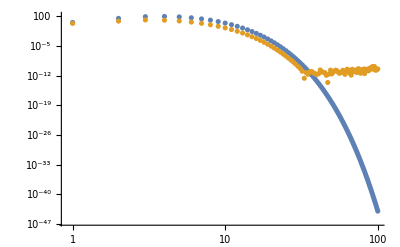

```mathematica
ListLogLogPlot[{Abs[integral],error}]
```

```mathematica
(* (2nd derivative) *)
```

```mathematica
Evaluate[D[f[y],{y,2}]]
```

(√n (-4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x)^2+4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x) (-x+y)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)))/(√(2 π))

```mathematica
(√n (-4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x)^2+4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x) (-x+y)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)))/(√(2 π))/.g1->1  /. g2->1+1/n
```

(√n (-4 ⅇ^(-2 n (1-x) (1+1/n-y)-1/2 n (-x+y)^2) n^2 (1-x)^2+4 ⅇ^(-2 n (1-x) (1+1/n-y)-1/2 n (-x+y)^2) n^2 (1-x) (-x+y)+(1-ⅇ^(-2 n (1-x) (1+1/n-y))) (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)))/(√(2 π))

```mathematica
(√n (-4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x)^2+4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x) (-x+y)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)))/(√(2 π))/.y->g2
```

(√n (-4 ⅇ^(-1/2 n (g2-x)^2) n^2 (g1-x)^2+4 ⅇ^(-1/2 n (g2-x)^2) n^2 (g1-x) (g2-x)))/(√(2 π))

```mathematica
Manipulate[Plot3D[{(√n (-4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x)^2+4 ⅇ^(-2 n (g1-x) (g2-y)-1/2 n (-x+y)^2) n^2 (g1-x) (-x+y)+(1-ⅇ^(-2 n (g1-x) (g2-y))) (-ⅇ^(-1/2 n (-x+y)^2) n+ⅇ^(-1/2 n (-x+y)^2) n^2 (-x+y)^2)))/(√(2 π))/.g1->1  /. g2->1+1/n,(√n (-4 ⅇ^(-1/2 n (g2-x)^2) n^2 (g1-x)^2+4 ⅇ^(-1/2 n (g2-x)^2) n^2 (g1-x) (g2-x)))/(√(2 π))/.g1->1  /. g2->1+1/n},{x,-3,1},{y,-3,1},PlotRange->{{-3,1},{-3,1},{-1,30}}],{n,1,30,1}]
```

```mathematica
(* (3rd derivative) h = n^(-1/2) is just enough to ensure convergence. This h makes rp (blue) the same order as the dominant error (in the yellow). Multiplied 3rd derivative by h^2= 1/n*)
```

```mathematica
Evaluate[D[f[y],{y,3}]]/. y-> g2
```

1/(√(2 π))√n (-6 n (-ⅇ^(-1/2 n (g2-x)^2) n+ⅇ^(-1/2 n (g2-x)^2) n^2 (g2-x)^2) (g1-x)-8 ⅇ^(-1/2 n (g2-x)^2) n^3 (g1-x)^3+12 ⅇ^(-1/2 n (g2-x)^2) n^3 (g1-x)^2 (g2-x))

```mathematica
Manipulate[Plot[{1/(√(2 π))√n (-6 n (-ⅇ^(-1/2 n (g2-x)^2) n+ⅇ^(-1/2 n (g2-x)^2) n^2 (g2-x)^2) (g1-x)-8 ⅇ^(-1/2 n (g2-x)^2) n^3 (g1-x)^3+12 ⅇ^(-1/2 n (g2-x)^2) n^3 (g1-x)^2 (g2-x))*1/n/.g1->1  /. g2->1+1/n,-ⅇ^(-1/2 n (g2-x)^2) n^(3/2) √(2/π) (g1-x)/.g1->1/.g2->1+1/n},{x,-3,1},PlotRange->Full],{n,1,100,1}]
```

```mathematica
Manipulate[Plot[1/(√(2 π))√n (-6 n (-ⅇ^(-1/2 n (g2-x)^2) n+ⅇ^(-1/2 n (g2-x)^2) n^2 (g2-x)^2) (g1-x)-8 ⅇ^(-1/2 n (g2-x)^2) n^3 (g1-x)^3+12 ⅇ^(-1/2 n (g2-x)^2) n^3 (g1-x)^2 (g2-x))*1/n^2/.g1->1  /. g2->1+1/n,{x,-3,1},PlotRange->Full],{n,2,100,1}]
```

```mathematica
Evaluate[D[f[y],{y,5}]]/. y-> g2
```

1/(√(2 π))√n (-10 n (3 ⅇ^(-1/2 n (g2-x)^2) n^2-6 ⅇ^(-1/2 n (g2-x)^2) n^3 (g2-x)^2+ⅇ^(-1/2 n (g2-x)^2) n^4 (g2-x)^4) (g1-x)-40 n^2 (3 ⅇ^(-1/2 n (g2-x)^2) n^2 (g2-x)-ⅇ^(-1/2 n (g2-x)^2) n^3 (g2-x)^3) (g1-x)^2-80 n^3 (-ⅇ^(-1/2 n (g2-x)^2) n+ⅇ^(-1/2 n (g2-x)^2) n^2 (g2-x)^2) (g1-x)^3-32 ⅇ^(-1/2 n (g2-x)^2) n^5 (g1-x)^5+80 ⅇ^(-1/2 n (g2-x)^2) n^5 (g1-x)^4 (g2-x))

```mathematica
(* h = n^(-1/2) is just enough to ensure convergence, multiplying 5th derivative by h^4= 1/n^2 *)
```

```mathematica
Manipulate[Plot[{1/(√(2 π))√n (-10 n (3 ⅇ^(-1/2 n (g2-x)^2) n^2-6 ⅇ^(-1/2 n (g2-x)^2) n^3 (g2-x)^2+ⅇ^(-1/2 n (g2-x)^2) n^4 (g2-x)^4) (g1-x)-40 n^2 (3 ⅇ^(-1/2 n (g2-x)^2) n^2 (g2-x)-ⅇ^(-1/2 n (g2-x)^2) n^3 (g2-x)^3) (g1-x)^2-80 n^3 (-ⅇ^(-1/2 n (g2-x)^2) n+ⅇ^(-1/2 n (g2-x)^2) n^2 (g2-x)^2) (g1-x)^3-32 ⅇ^(-1/2 n (g2-x)^2) n^5 (g1-x)^5+80 ⅇ^(-1/2 n (g2-x)^2) n^5 (g1-x)^4 (g2-x))*1/n^2/.g1->1  /. g2->1+1/n,-ⅇ^(-1/2 n (g2-x)^2) n^(3/2) √(2/π) (g1-x)/.g1->1/.g2->1+1/n},{x,-3,1},PlotRange->Full],{n,1,100,1}]
```